```mathematica
Simplify[(1+d*(b-1))*(1-x2-x3) + (1+d*(b-1))*x2 + (1-d+d^2)*x3]
```

1+d^2 x3+d (-1+b-b x3)

```mathematica
fD[xD_,xG1_,xC1_,delta_]:=xD*((1-xC1)*(1/(1-delta))+xC1*(1+delta));fC1[xD_,xG1_,xC1_,delta_]:=xC1*((1-xD)*(1/(1-delta))+xD*(1+delta));fG1[xD_,xG1_,xC1_,delta_]:=(1-xC1-xD)*(1/(1-delta));SPtoPop[xD_,xG1_,xC1_,delta_]:= {fD[xD,xG1,xC1,delta]/(fD[xD,xG1,xC1,delta]+fC1[xD,xG1,xC1,delta]+fG1[xD,xG1,xC1,delta]),fG1[xD,xG1,xC1,delta]/(fD[xD,xG1,xC1,delta]+fC1[xD,xG1,xC1,delta]+fG1[xD,xG1,xC1,delta]),fC1[xD,xG1,xC1,delta]/(fD[xD,xG1,xC1,delta]+fC1[xD,xG1,xC1,delta]+fG1[xD,xG1,xC1,delta])}
```

```mathematica
SPtoPop[0.4,0.3,0.3,0.9]
```

{0.375869,0.372393,0.251738}

```mathematica
Total[{0.3758689175769613,0.37239324726911616,0.2517378351539225}]
```

1.

```mathematica
(*known quantities x1,x2,x3,and the endogenous break probabilities eb*)
(*the overall outflow per game is*)

(* x33 = 1-x11-x12-x13-x22-x23*)
(*DEN0 is the overall outflow*)
(*x11 = x1 - (1/2)*(x12+x13) *)
(*x22 = x2 - (1/2)*(x12+x23) *)
(*x33 = x3 - (1/2)*(x13+x23) *)
(* solve for x12,x13,x23*)

DEN0 = b11*x11+ b12*x12 +b13*x13 + b22*x22 + b23 *x23 + b33*x33;

DEN = DEN0/.x33 -> 1-x11-x12-x13-x22-x23
b11 x11+b12 x12+b13 x13+b22 x22+b33 (1-x11-x12-x13-x22-x23)+b23 x23
DEN1 = DEN /. {x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2)
Simplify[DEN1]
1/2 (2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))
(*Proportions in singles pool of types 1,2 and 3*)
PS1 =((b11*x11 + (1/2)*b12*x12+ (1/2)*b13*x13)/DEN1  )  /.{x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
((b12 x12)/2+b11 (x1+1/2 (-x12-x13))+(b13 x13)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))
PS2 =((b22*x22 + (1/2)*b12*x12+ (1/2)*b23*x23)/DEN1) /.{x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
((b12 x12)/2+b22 (x2+1/2 (-x12-x23))+(b23 x23)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))
PS3 =((b33*x33 + (1/2)*b13*x13+ (1/2)*b23*x23)/DEN1) /.{x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
((b13 x13)/2+(b23 x23)/2+b33 (1/2 (-x13-x23)+x3))/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))
eq1=Simplify[b12*x12==2*PS1*PS2*DEN1]
b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))
eq2=Simplify[b23*x23==2*PS2*PS3*DEN1]
b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))
eq3=Simplify[b13*x13==2*PS1*PS3*DEN1]
b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))
solveSystem[x1_?NumericQ,x2_?NumericQ,x3_?NumericQ,delta_?NumericQ]:=Module[{b11,b12,b13,b22,b23,b33,eq1,eq2,eq3,sol,solution},
(*Define b values*)b11=b12=b22=b23=b33=(1-delta); 
b13=1/(1+delta);
eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));

(*Solve the system numerically for positive roots that satisfy all conditions*)sol=Which[x1>0&&x2>0&&x3>0,NSolve[{eq1,eq2,eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals],x1==0&&x2==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x2==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0,NSolve[{eq2,x12==0,x23>0,x13==0},{x12,x23,x13},Reals],x2==0,NSolve[{eq3,x12==0,x23==0,x13>0},{x12,x23,x13},Reals],x3==0,NSolve[{eq1,x12>0,x23==0,x13==0},{x12,x23,x13},Reals]];

(*If[Length[sol]==1,Print["solveSystem failed with insufficient parts: ",{x1,x2,x3,delta}];Throw[$Failed]]*)
(*Use the first solution*)solution=sol[[1]];
(*Return the six values as specified*){x1-(1/2)*(x12+x13),x12,x13,x2-(1/2)*(x12+x23),x23,x3-(1/2)*(x23+x13)}/.solution];
solveSystem[0.4,0,0.6,0.9]


xdd[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[1]]
xddc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[2]]
xdc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[3]]
xdcdc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[4]]
xdcc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[5]]
xc1c1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[6]]

xdd[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[1]]
xddc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[2]]
xdc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[3]]
xdcdc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[4]]
xdcc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[5]]
xc1c1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[6]]

(*against d -> 0, against CD -> play (1/(1-delta)) periods. The first accounts for 1/(1/(1-delta)) and earns nothing, the rest accounts for (delta/(1-delta))/(1/(1-delta))  of that time and yields b per period, against C1, 2 periods are played, and the total duration is 1+delta. the first yields zero payoff. the second accounts for delta/(1+delta) and yields b  *)
```

b11 x11+b12 x12+b13 x13+b22 x22+b33 (1-x11-x12-x13-x22-x23)+b23 x23

b11 x11+b12 x12+b13 x13+b22 x22+b33 (1-x11-x12-x13-x22-x23)+b23 x23

b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2)

b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2)

1/2 (2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

1/2 (2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

((b12 x12)/2+b11 (x1+1/2 (-x12-x13))+(b13 x13)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

((b12 x12)/2+b11 (x1+1/2 (-x12-x13))+(b13 x13)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

((b12 x12)/2+b22 (x2+1/2 (-x12-x23))+(b23 x23)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

((b12 x12)/2+b22 (x2+1/2 (-x12-x23))+(b23 x23)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

((b13 x13)/2+(b23 x23)/2+b33 (1/2 (-x13-x23)+x3))/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

((b13 x13)/2+(b23 x23)/2+b33 (1/2 (-x13-x23)+x3))/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

{0.322087,0,0.155827,0,0,0.522087}

```mathematica
PG1[xD_,xG1_, b_,c_,delta_] := Piecewise[{{(1/xG1)*(xddc[xD,xG1,delta]*(delta*(-c)/(1/(1-delta)))+(2*xdcdc[xD,xG1,delta]+xdcc1[xD,xG1,delta])*(delta)*(b-c)),xG1>0},{0,xG1≤0}}]
```

```mathematica
(*PD = ((1/(1-delta))*xD + (1+b+(delta^2/(1-delta))*xG1  +  (1-xD-xG1)*(1+delta*b))/((1/(1-delta)) * (xD) + (1/(1-delta)) * (xG1) + (1+delta) * (1-xD-xG1)))
(*
```

```mathematica
{xdd[0.2,0.3,0.8],xddc[0.2,0.3,0.8],xdc1[0.2,0.3,0.8]}
```

{0.0728014,0.148515,0.105882}

```mathematica
Total[{2*0.0728014,0.1485148514851485,0.10588235294117647}]
```

0.4

```mathematica
PD[xD_,xG1_, b_,c_,delta_] := Piecewise[{{(1/xD)*(xddc[xD,xG1,delta]*(delta*(b)/(1/(1-delta))) + xdc1[xD,xG1,delta]*b*(delta/(1+delta))),xD>0},{0,xD≤0}}]
```

```mathematica
(*PD[xD_,xG1_, b_,c_,delta_] :=((1/(1-delta))*xD + (1+(b+1)+(delta^2/(1-delta)))*xG1  +  (1-xD-xG1)*(1+delta*(b+1)))/((1/(1-delta)) * (xD) + (1/(1-delta)) * (xG1) + (1+delta) * (1-xD-xG1))
PD[xD_,xG1_, b_,c_,delta_] :=Piecewise[{{(1/xD)*(1/2)*(xddc[xD,xG1,delta]*delta*b+xdc1[xD,xG1,delta]*b*(delta/(1+delta))),xD>0},{0,xD==0}}]
```

```mathematica
PC1[xD_,xG1_, b_,c_,delta_] :=Piecewise[{{(1/(1-xD-xG1))*(xdc1[xD,xG1,delta]*(delta*(-c)/(1+delta))+(2*xc1c1[xD,xG1,delta]+xdcc1[xD,xG1,delta])*(delta)*(b-c)),1-xG1-xD>0},{0,1-xG1-xD≤0}}];

AvgP[xD_,xG1_, b_,c_,delta_] := xD* PD[xD,xG1, b,c,delta] + xG1* PG1[xD,xG1, b,c,delta] + (1-xD-xG1)* PC1[xD,xG1, b,c,delta];
```

```mathematica
PG1[0.1,0.7, 3,1,0.8]
```

PG1[0.1,0.7,3,1,0.8]

```mathematica
PC1[0.1,0.7, 3,1,0.8]
```

3.02244

```mathematica
(0.8)*(b-1)
```

1.6

```mathematica
{xdc1[0.1,0.7,0.8],xdcc1[0.1,0.7,0.8],xc1c1[0.1,0.7,0.8]}
```

{0.0173704,0.292581,0.0450242}

```mathematica
Total[{0.017370350344673793,0.29258134191621715,0.045024153869554606}]
```

0.354976

```mathematica
0.8*(-1)/(1+0.8)
```

-0.444444

```mathematica
(1/(1-0.1-0.7))*(xdc1[0.1,0.7,0.8]*(0.8*(-1)/(1+0.8))+(2*xdcdc[0.1,0.7,0.8]+xdcc1[0.1,0.7,0.8])*(0.8)*(b-1))
Simplex2DCoord[{0, 1,0 }]
```

9.9072

{1,0}

```mathematica
Simplex2DCoord[{x1_, x2_, x3_}] :=x1*{0, 0} + x2*{1, 0} + x3*{1/2, √3/2}
```

```mathematica
Simplex2DInverseCoord[{y1_,y2_}]:={1,0,0}+y1*{-1,1,0}+y2*{-1/√3,-1/√3,2/√3}
```

```mathematica
(*ExpectedChange[x_, b_,c_,delta_]:={(x.{1,0,0})*(PD[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),(x.{0,1,0})*(PDC[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),(x.{0,0,1})*(PC1[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta])}
```

```mathematica
(*ExpectedChange[x_,b_,c_,delta_]:={Piecewise[{{(x.{1,0,0})*(PD[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{1,0,0}<1}},0],Piecewise[{{(x.{0,1,0})*(PDC[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,1,0}<1}},0],Piecewise[{{(x.{0,0,1})*(PC1[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,0,1}<1}},0]}
ExpectedChange[{0.2,0.6,0.2}, 3,1,0.9]
PD[0.8,0.2,3,1,0.9]
PDC[0.8,0.2,3,1,0.9]*)
ExpectedChange[x_List,b_?NumericQ,c_?NumericQ,delta_?NumericQ]:=Module[{change},If[VectorQ[x,NumericQ],(*If all elements of x are numeric,compute the change*)change={Piecewise[{{(x.{1,0,0})*(PD[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{1,0,0}<1}},0],Piecewise[{{(x.{0,1,0})*(PG1[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,1,0}<1}},0],Piecewise[{{(x.{0,0,1})*(PC1[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,0,1}<1}},0]},(*Otherwise,return some default value or error*)Throw["Non-numeric input in x"]];
change]
ExpectedChange[{0.2,0.6,0.2}, 3,1,0.9]
ExpectedChange[{0.1,0.45,0.45}, 3,1,0.9]
```

{-0.382791,0.195367,0.187425}

{-0.227574,0.0243037,0.20327}

```mathematica
Trajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
BackwardTrajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==-ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
BackTrajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==-ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"},StepMonitor:>Print["Step to ",ti,": ",x[ti],"  ExpectedChange ",-ExpectedChange[x[ti], b,c,delta]]]
]
```

```mathematica
Trajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
Outside = Graphics[{EdgeForm[Thick],FaceForm[{White}],Opacity[1], Polygon[{{Simplex2DCoord[{1, 0, 0}],Simplex2DCoord[{0, 1, 0}],Simplex2DCoord[{0, 0, 1}]}}],Boxed->False}];
```

```mathematica
Total[{0.09316261365479597,-0.13967751062179704,0.04651489696700084}]
```

-2.22045×10^-16

```mathematica
ExpectedChange[{0.1,0.45,0.45}, 3,1,0.8]
```

{-0.14066,0.0711832,0.0694771}

```mathematica
ExpectedChange[{0.1,0.2,0.2},3,1,0.8]
```

{0.0250061,0.296545,-0.0918716}

```mathematica
%132[40]
```

```mathematica
{{0.9497241727157818,0.,0.05027582728419761}} (*the intersection point if starting at 0.8*)
```

```mathematica
{0.7528964283105991,0.,0.2471035716894052}(*the intersection point if starting at 0.6*)
```

```mathematica
{0.9877308983271877,0.,0.01226910167275589} (*the intersection point if starting at 0.9*)
```

```mathematica
%343[2]
```

```mathematica
ExpectedChange[{0.36967132485506154,0.6122566683499397,0.01807200679499883},3,1,0.9]
```

{-0.927422,-0.404168,1.33159}

```mathematica
Total[{0.36967132485506154,0.6122566683499397,0.01807200679499883}]
```

1.

```mathematica
deltav = 0.8
```

0.8

```mathematica
Trajectory[N[{1/3,1/3,1/3}],3,1,0.8,1]
```

InterpolatingFunction[…]

```mathematica
%300[0.2]
```

```mathematica
Simplex2DCoord[{0.28381266039704006,0.3589633558974369,0.35722398370552255}]
```

{0.537575,0.309365}

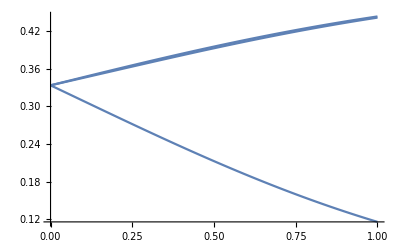

```mathematica
Plot[%300[x],{x,0.,1.}]
```

```mathematica
0.8



(*bv = 2;cv=1;deltav=0.9;Tv = 100;div=10;
listOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,Tv][ti]],{initx1,0,1,1/div},{initx2,0,1-initx1,1/div}]];*)

bv = 3;cv=1;deltav=0.8;Tv = 6;div=10;
listOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,Tv][ti]],{initx1,1/div,(div-1)/div,1/div},{initx2,1/div,1-initx1-1/div,1/div}]];
```

0.8

```mathematica
bottomleftlistOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,Tv][ti]],{initx1,0.92,1,10},{initx2,0.04,1,10}]];
```

```mathematica
lowerbottomleftlistOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,5*Tv][ti]],{initx1,0.94,1,15},{initx2,0.03,1,10}]];
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {0.999928+1/2 (-x12-x13),x12,x13,0.000071901+1/2 (-x12-x23),x23,3.47119×10^-9+1/2 (-x13-x23)}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {0.0000229914-0.999928 (0.0000719097 (0.48 Part[«2»]+1.33333 Part[«2»])-1. (-0.16 Part[«2»]+1.6 Plus[«2»])-1. (-0.444444 Part[«2»]+1.6 Plus[«2»])),«1»,-5.33786×10^-9-3.47121×10^-9 (-1. (0.48 Part[«2»]+1.33333 Part[«2»])-«1»+2.88086×10^8 (-«19» «1»+«1»))} is not a list of numbers with dimensions {3} at {ti,x$14644991[ti],x$14644991'[ti]} = {22.4592,{0.999928,0.000071901,3.47121×10^-9},{0.0000229914,-0.0000229861,-5.33786×10^-9}}.

```mathematica
listOfProjectedTrajectories
```

{Simplex2DCoord[InterpolatingFunction[…][ti]]}

```mathematica
2 d^2 x11-d^4 x11+√(x11-2 d^2 x11+d^4 x11-2 d^2 x11^2+5 d^4 x11^2-4 d^6 x11^2+d^8 x11^2)
```

```mathematica
BottomExpectedChange[x_List,b_?NumericQ,c_?NumericQ,delta_?NumericQ]:=Module[{change},If[VectorQ[x,NumericQ],(*If all elements of x are numeric,compute the change*)change={(x.{1,0,0})*((x.{0,1,0})*delta*b - ((x.{1,0,0})*(x.{0,1,0})*delta*b + (x.{0,1,0})*((x.{0,1,0})*(delta/(1-delta))*(b-c)-(x.{1,0,0})*delta*c))),-(x.{1,0,0})*((x.{0,1,0})*delta*b - ((x.{1,0,0})*(x.{0,1,0})*delta*b + (x.{0,1,0})*((x.{0,1,0})*(delta/(1-delta))*(b-c)-(x.{1,0,0})*delta*c))),0},(*Otherwise,return some default value or error*)Throw["Non-numeric input in x"]];
change]
```

```mathematica
BottomExpectedChange[{0.99,0.01,0}, 3,1,0.8]
```

{0.0072864,-0.0072864,0}

```mathematica
BottomTrajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==BottomExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
listOfProjectedTrajectoriesBottom=Flatten[Table[Simplex2DCoord[BottomTrajectory[N[{initx1,1-initx1,0}],bv,cv,deltav,0.01][ti]],{initx1,1/div,(div-2)/div,1/div}]];
```

```mathematica
extraleftlistOfProjectedTrajectoriesBottom=Flatten[Table[Simplex2DCoord[BottomTrajectory[N[{initx1,1-initx1,0}],bv,cv,deltav,0.01][ti]],{initx1,(div-0.5)/div,1,20}]];
```

```mathematica
extraleftlistOfProjectedTrajectoriesBottom
```

{Simplex2DCoord[InterpolatingFunction[…][ti]]}

```mathematica
ExpectedChange[{0.5,0,0.5}, 3,1,0.8]
```

{-0.352941,0,0.352941}

```mathematica
div=10;stepSize=0.01;(*Small step size for the direction*)(*Generate the list of initial 3D points*)initialPoints=Table[{initx1,0,1-initx1},{initx1,1/div,(div-1)/div,1/div}];

(*Compute the expected change and create arrows*)
leftarrows=Map[Function[point,Module[{change,endPoint},change=ExpectedChange[point,bv,cv,deltav];(*Compute the expected change*)endPoint=point+stepSize*change;(*Calculate the new point by applying the change*)(*Convert both the initial and end point to 2D using Simplex2DCoord*){Arrowheads[0.02],Arrow[{Simplex2DCoord[point],Simplex2DCoord[endPoint]}]}]],initialPoints];
```

```mathematica
div=1;stepSize=0.01;(*Small step size for the direction*)(*Generate the list of initial 3D points*)initialPoints=Table[{initx1,0,1-initx1},{initx1,0.985,1,1/div}];

(*Compute the expected change and create arrows*)
bottomleftarrows=Map[Function[point,Module[{change,endPoint},change=ExpectedChange[point,bv,cv,deltav];(*Compute the expected change*)endPoint=point+stepSize*change;(*Calculate the new point by applying the change*)(*Convert both the initial and end point to 2D using Simplex2DCoord*){Arrowheads[0.02],Arrow[{Simplex2DCoord[point],Simplex2DCoord[endPoint]}]}]],initialPoints];
```

```mathematica
bottomleftarrows
```

{{Arrowheads[0.02],Arrow[{{0.0075,0.0129904},{0.00746096,0.0129228}}]}}

```mathematica
bv=3;cv=1;div = 10;ax =0.03;backtraj=Flatten[Table[Simplex2DCoord[BackwardTrajectory[N[{1-ax,initx1,ax-initx1}],bv,cv,deltav,10][ti]],{initx1,ax*1/div,ax*(div-1)/div,ax*1/div}]]
```

$Aborted

Show::gcomb: Could not combine the graphics objects in ….

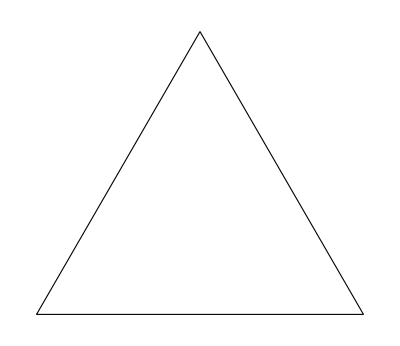
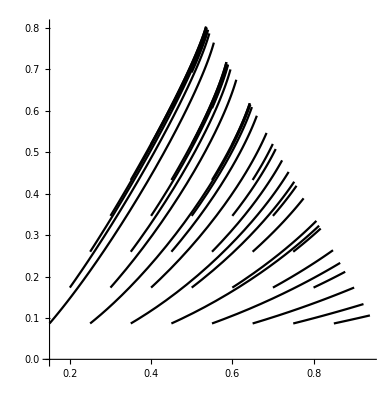
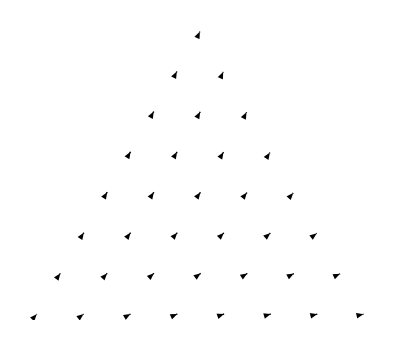
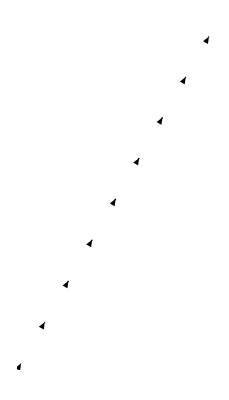
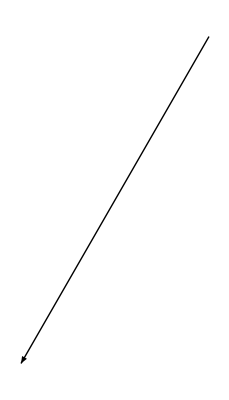
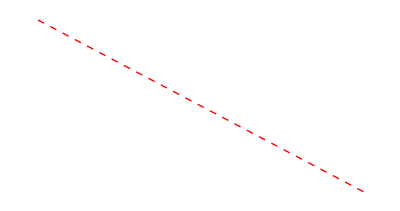
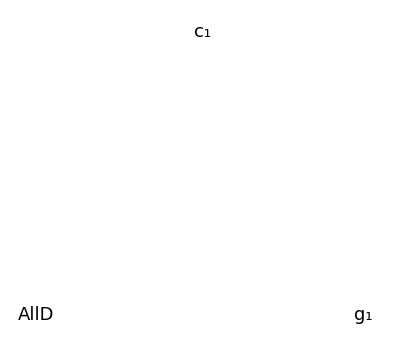
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,lowerbottomleftgraphWithTrajectories,Neutralpartx,-Graphics-,-Graphics-},Frame→False,Axes→False,ImageSize→Large]

```mathematica
listOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,listOfProjectedTrajectories],1];listOfArrowsBottom=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,listOfProjectedTrajectoriesBottom],1];graphWithTrajectories=ParametricPlot[Evaluate[listOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];(*bottomleftlistOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.1)}]},{i,0,0}]&,bottomleftlistOfProjectedTrajectories],1];bottomleftgraphWithTrajectories=ParametricPlot[Evaluate[bottomleftlistOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];lowerbottomleftlistOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.1)}]},{i,0,0}]&,lowerbottomleftlistOfProjectedTrajectories],1];lowerbottomleftgraphWithTrajectories=ParametricPlot[Evaluate[lowerbottomleftlistOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];*)Show[{Outside,graphWithTrajectories,Graphics[listOfArrows],Graphics[leftarrows],Graphics[bottomleftarrows],Graphics[listOfArrowsBottom],lowerbottomleftgraphWithTrajectories,Neutralpartx,
Neutralpart =Graphics[{Red,Dashed,Line[{Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),1-((bv-1)/(bv-deltav)),0,deltav]],Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),0,1-((bv-1)/(bv-deltav)),deltav]]}]}],Graphics[{Inset[Style[Row[{Subscript["c",1]}],18],{0.505,0.9}],Inset[Style[Row[{"AllD"}],18],{-0.04,-0.035}],Inset[Style[Row[{Subscript["g",1]}],18],{1.035,-0.035}]}]},Frame ->False,Axes->False,ImageSize->Large]
```

```mathematica
s
```

```mathematica
lowerbottomleftgraphWithTrajectories
```

lowerbottomleftgraphWithTrajectories

```mathematica
listOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,listOfProjectedTrajectories],1];listOfArrowsBottom=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,listOfProjectedTrajectoriesBottom],1];ELlistOfArrowsBottom=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,extraleftlistOfProjectedTrajectoriesBottom],1];graphWithTrajectories=ParametricPlot[Evaluate[listOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];bottomleftlistOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.1)}]},{i,0,0}]&,bottomleftlistOfProjectedTrajectories],1];bottomleftgraphWithTrajectories=ParametricPlot[Evaluate[bottomleftlistOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];lowerbottomleftlistOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.1)}]},{i,0,0}]&,lowerbottomleftlistOfProjectedTrajectories],1];lowerbottomleftgraphWithTrajectories=ParametricPlot[Evaluate[lowerbottomleftlistOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];Show[{Outside,graphWithTrajectories,Graphics[listOfArrows],Graphics[leftarrows],Graphics[ELlistOfArrowsBottom],Graphics[bottomleftarrows],Graphics[listOfArrowsBottom],
Neutralpart =Graphics[{Red,Thick,Line[{Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),1-((bv-1)/(bv-deltav)),0,deltav]],Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),0,1-((bv-1)/(bv-deltav)),deltav]]}]}],Neutralpartx,Graphics[{Inset[Style[Row[{Subscript["c",1]}],18],{0.505,0.9}],Inset[Style[Row[{"AllD"}],18],{-0.04,-0.035}],Inset[Style[Row[{Subscript["g",1]}],18],{1.035,-0.035}]}]},Frame ->False,Axes->False,ImageSize->Large]
```

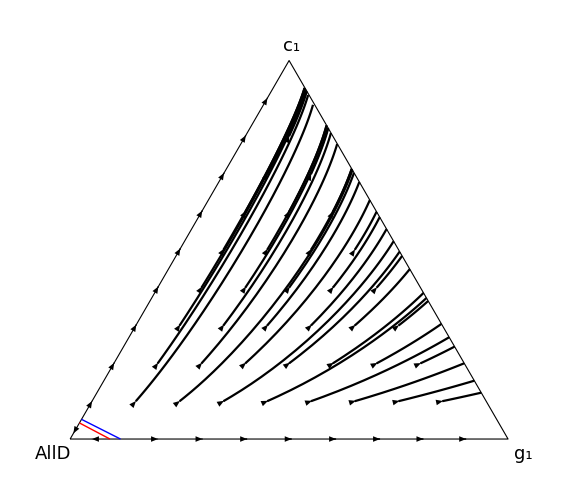

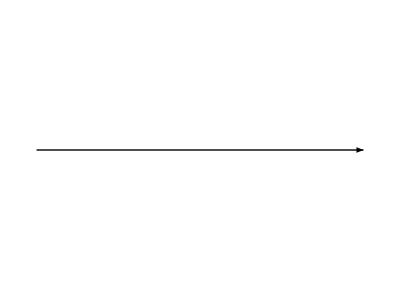

```mathematica
Show[Graphics[ELlistOfArrowsBottom]]
```

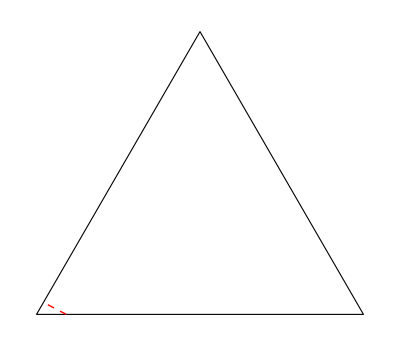

```mathematica
deltav=0.8;Neutralpart =Graphics[{Red,Dashed,Line[{Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),1-((bv-1)/(bv-deltav)),0,deltav]],Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),0,1-((bv-1)/(bv-deltav)),deltav]]}]}];Show[Outside,Neutralpart]
```

```mathematica
Trajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
BackTrajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==-ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
bv = 2;cv=1;deltav=0.8;Tv = 60;div = 10;
listOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,Tv][ti]],{initx1,0,1,1/div},{initx2,0,1-initx1,1/div}]];listOfProjectedTrajectoriesBACK=Flatten[Table[Simplex2DCoord[BackTrajectory[N[{(-cv+bv deltav)/((bv-cv) deltav)-0.0001,0.0002,1-(-cv+bv deltav)/((bv-cv) deltav)-0.0001}],bv,cv,deltav,Tv][ti]],{initx1,0,1,10},{initx2,0,1-initx1,10}]];
```

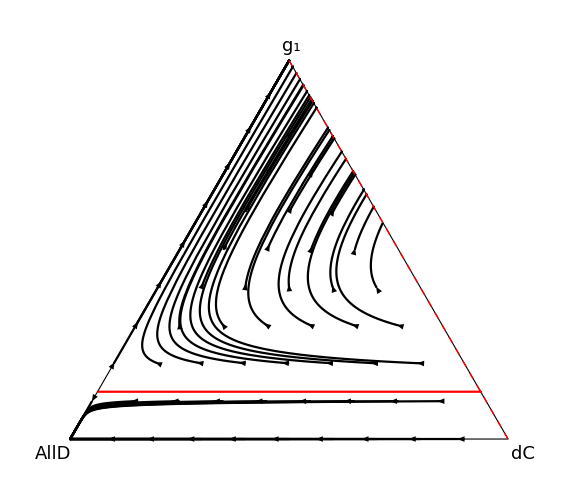

```mathematica
listOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.2)}]},{i,0,0}]&,listOfProjectedTrajectories],1];graphWithTrajectories=ParametricPlot[Evaluate[listOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];
graphWithTrajectoriesBACK=ParametricPlot[Evaluate[listOfProjectedTrajectoriesBACK],{ti,0,Tv},PlotStyle ->Red];Neutralpart =Graphics[{Red,Dashed,Line[{Simplex2DCoord[{0,1,0}],Simplex2DCoord[{0,0,1}]}]}]; 
Show[{Outside,graphWithTrajectories,graphWithTrajectoriesBACK,Graphics[listOfArrows],Neutralpart,Graphics[{Inset[Style[Row[{Subscript["g",1]}],18],{0.505,0.9}],Inset[Style[Row[{"AllD"}],18],{-0.04,-0.035}],Inset[Style[Row[{"dC"}],18],{1.035,-0.035}]}]},Frame ->False,Axes->False,ImageSize->Large]
```

```mathematica
backwlistOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,backtraj],1];graphWithTrajectories=ParametricPlot[Evaluate[backtraj],{ti,0,10},PlotStyle ->Black];
```

```mathematica
Neutralpartx =Graphics[{Blue,Thick,Line[{Simplex2DCoord[{0.885,0.115,0}],Simplex2DCoord[{0.948,0,0.052}]}]}];Show[{Outside,graphWithTrajectories,Graphics[backwlistOfArrows],Neutralpartx}]
```

-Graphics-

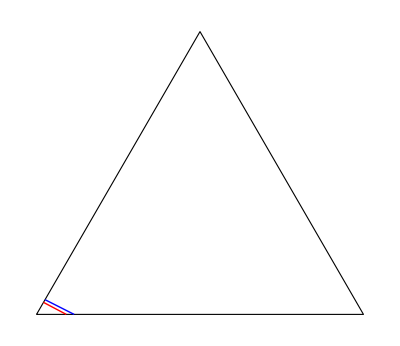

```mathematica
Show[Outside,Neutralpartx,Neutralpart =Graphics[{Red,Thick,Line[{Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),1-((bv-1)/(bv-deltav)),0,deltav]],Simplex2DCoord[SPtoPop[((bv-1)/(bv-deltav)),0,1-((bv-1)/(bv-deltav)),deltav]]}]}]]
```